#### Force debug

#1 excluded volume force between bead-bead

```mathematica
ClearAll[a,Nks,T,KB,bk,Ss2,ev,r]
a=0.077;(*um*)
Nks=19.8;(*non-unit*)
T=297;(*Kelvin*)
KB=1.380662*10^(-17);(*N*um/K*)
bk = 0.106;(*um*)
Ss2 = Nks*bk^2/6;(*um^2*)
ev= 2.62851(*dimensionless*);
ev=ev*a^3;(*um^3*)
```

====> pp_ev_gaussian = ‘c1 c2’

```mathematica
Clear[c1,c2,fppevgaussianMat,r];
c1=1.5;c2=1.5;
r=2.1*{{Cos[Pi/3]*Sin[Pi/3],Cos[Pi/3]*Cos[Pi/3],Sin[Pi/3]},{0.,0.,0.},-{Cos[Pi/3]*Sin[Pi/3],Cos[Pi/3]*Cos[Pi/3],Sin[Pi/3]}}
```

{{0.909327,0.525,1.81865},{0.,0.,0.},{-0.909327,-0.525,-1.81865}}

```mathematica
fppevgaussian[c1_,c2_,rij_]:=c1*c2*Exp[-c2*Norm[rij]^2]*rij;(*rij = ri-rj*)
fppevgaussianMat=Table[If[i≠j,fppevgaussian[c1,c2,r[[i]]-r[[j]]],{0,0,0}],{i,1,Length@r},{j,1,Length@r}]
```

{{{0,0,0},{0.00274185,0.00158301,0.00548371},{1.31978×10^-11,7.61973×10^-12,2.63955×10^-11}},{{-0.00274185,-0.00158301,-0.00548371},{0,0,0},{0.00274185,0.00158301,0.00548371}},{{-1.31978×10^-11,-7.61973×10^-12,-2.63955×10^-11},{-0.00274185,-0.00158301,-0.00548371},{0,0,0}}}

```mathematica
%//MatrixForm
```

((0
0
0) | (0.00274185
0.00158301
0.00548371) | (1.31978×10^-11
7.61973×10^-12
2.63955×10^-11)
(-0.00274185
-0.00158301
-0.00548371) | (0
0
0) | (0.00274185
0.00158301
0.00548371)
(-1.31978×10^-11
-7.61973×10^-12
-2.63955×10^-11) | (-0.00274185
-0.00158301
-0.00548371) | (0
0
0))

```mathematica
fppevgaussianParticle=Total[fppevgaussianMat,{-2}]
```

{{0.00274185,0.00158301,0.00548371},{0.,0.,0.},{-0.00274185,-0.00158301,-0.00548371}}

```mathematica
%//MatrixForm
```

(0.00274185 | 0.00158301 | 0.00548371
0. | 0. | 0.
-0.00274185 | -0.00158301 | -0.00548371)

====> pp_ev_gaussian_polymerChain = ‘ev’

```mathematica
Clear[c1,c2,r];
c1=ev*Nks^2*(3/(4*Pi*Ss2))^1.5;
c2=(3 a^2)/(4Ss2);
r=2.1*{{Cos[Pi/3]*Sin[Pi/3],Cos[Pi/3]*Cos[Pi/3],Sin[Pi/3]},{0.,0.,0.},-{Cos[Pi/3]*Sin[Pi/3],Cos[Pi/3]*Cos[Pi/3],Sin[Pi/3]}}
```

{{0.909327,0.525,1.81865},{0.,0.,0.},{-0.909327,-0.525,-1.81865}}

```mathematica
fppevgaussianpolymerchain[rij_]:=c1*c2*Exp[-c2*Norm[rij]^2]*rij;(*rij=ri-rj*)
fppevgaussianpolymerchainMat=Table[If[i≠j,fppevgaussianpolymerchain[r[[i]]-r[[j]]],{0,0,0}],{i,1,Length@r},{j,1,Length@r}]
```

{{{0,0,0},{0.4939,0.285153,0.9878},{0.202117,0.116692,0.404233}},{{-0.4939,-0.285153,-0.9878},{0,0,0},{0.4939,0.285153,0.9878}},{{-0.202117,-0.116692,-0.404233},{-0.4939,-0.285153,-0.9878},{0,0,0}}}

```mathematica
%//MatrixForm
```

((0
0
0) | (0.4939
0.285153
0.9878) | (0.202117
0.116692
0.404233)
(-0.4939
-0.285153
-0.9878) | (0
0
0) | (0.4939
0.285153
0.9878)
(-0.202117
-0.116692
-0.404233) | (-0.4939
-0.285153
-0.9878) | (0
0
0))

```mathematica
fppevgaussianpolymerchainParticle=Total[fppevgaussianpolymerchainMat,{-2}]
```

{{0.696017,0.401845,1.39203},{0.,0.,0.},{-0.696017,-0.401845,-1.39203}}

```mathematica
%//MatrixForm
```

(0.696017 | 0.401845 | 1.39203
0. | 0. | 0.
-0.696017 | -0.401845 | -1.39203)

====> pp_ev_lj_cut = ‘epsilon sigma rcut’

```mathematica
Clear[epsilon,sigma,rcut,r,fppevljcut,fppevljcutMat,fppevljcutParticle];
epsilon=1;sigma=2.1;rcut=3;
r=2.1*{{Cos[Pi/3]*Sin[Pi/3],Cos[Pi/3]*Cos[Pi/3],Sin[Pi/3]},{0.,0.,0.},-{Cos[Pi/3]*Sin[Pi/3],Cos[Pi/3]*Cos[Pi/3],Sin[Pi/3]}}
```

{{0.909327,0.525,1.81865},{0.,0.,0.},{-0.909327,-0.525,-1.81865}}

```mathematica
fppevljcut[epsilon_,sigma_,rcut_,rij_]:= If[Norm[rij]≤rcut,24*epsilon*(2*sigma^12/Norm[rij]^12-sigma^6/Norm[rij]^6)*rij/Norm[rij]^2,{0,0,0}];
fppevljcutMat=Table[If[i≠j,fppevljcut[epsilon,sigma,rcut,r[[i]]-r[[j]]],{0,0,0}],{i,1,Length@r},{j,1,Length@r}]
```

{{{0,0,0},{4.94872,2.85714,9.89743},{0,0,0}},{{-4.94872,-2.85714,-9.89743},{0,0,0},{4.94872,2.85714,9.89743}},{{0,0,0},{-4.94872,-2.85714,-9.89743},{0,0,0}}}

```mathematica
%//MatrixForm
```

((0
0
0) | (4.94872
2.85714
9.89743) | (0
0
0)
(-4.94872
-2.85714
-9.89743) | (0
0
0) | (4.94872
2.85714
9.89743)
(0
0
0) | (-4.94872
-2.85714
-9.89743) | (0
0
0))

```mathematica
fppevljcutParticle=Total[fppevljcutMat,{-2}]
```

{{4.94872,2.85714,9.89743},{0.,0.,0.},{-4.94872,-2.85714,-9.89743}}

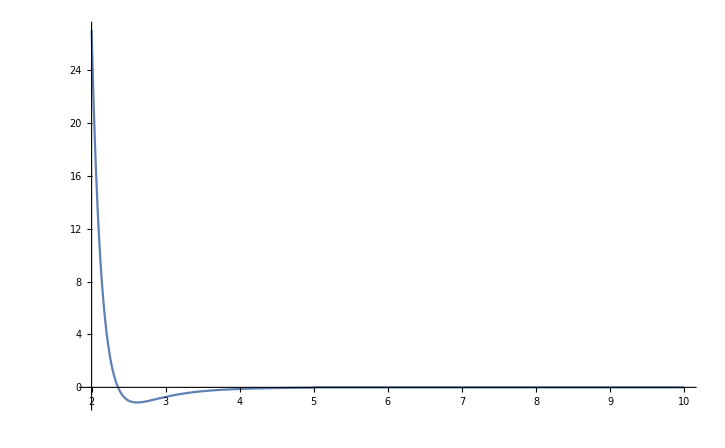

```mathematica
Plot[fppevljcut[1.0,2.1,5,{x,0,0}-{0,0,0}][[1]],{x,2,10},PlotRange->Full]
```

====> pp_ev_lj_repulsive = ‘epsilon sigma’

```mathematica
Clear[epsilon,sigma,r,fppevljrepulsive,fppevljrepulsiveMat,fppevljrepulsiveParticle];
epsilon=1;sigma=2.1;
r=2.1*{{Cos[Pi/3]*Sin[Pi/3],Cos[Pi/3]*Cos[Pi/3],Sin[Pi/3]},{0.,0.,0.},-{Cos[Pi/3]*Sin[Pi/3],Cos[Pi/3]*Cos[Pi/3],Sin[Pi/3]}}
```

{{0.909327,0.525,1.81865},{0.,0.,0.},{-0.909327,-0.525,-1.81865}}

```mathematica
fppevljrepulsive[epsilon_,sigma_,rij_]:= If[Norm[rij]≤2^(1/6)sigma,24*epsilon*(2*sigma^12/Norm[rij]^12-sigma^6/Norm[rij]^6)*rij/Norm[rij]^2,{0,0,0}];
fppevljrepulsiveMat=Table[If[i≠j,fppevljrepulsive[epsilon,sigma,r[[i]]-r[[j]]],{0,0,0}],{i,1,Length@r},{j,1,Length@r}]
```

{{{0,0,0},{4.94872,2.85714,9.89743},{0,0,0}},{{-4.94872,-2.85714,-9.89743},{0,0,0},{4.94872,2.85714,9.89743}},{{0,0,0},{-4.94872,-2.85714,-9.89743},{0,0,0}}}

```mathematica
%//MatrixForm
```

((0
0
0) | (4.94872
2.85714
9.89743) | (0
0
0)
(-4.94872
-2.85714
-9.89743) | (0
0
0) | (4.94872
2.85714
9.89743)
(0
0
0) | (-4.94872
-2.85714
-9.89743) | (0
0
0))

```mathematica
fppevljrepulsiveParticle=Total[fppevljrepulsiveMat,{-2}]
```

{{4.94872,2.85714,9.89743},{0.,0.,0.},{-4.94872,-2.85714,-9.89743}}

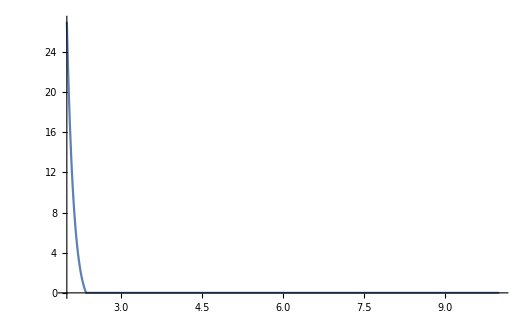

```mathematica
Plot[fppevljrepulsive[1.0,2.1,{x,0,0}-{0,0,0}][[1]],{x,2,10},PlotRange->Full]
```

====> pp_ev_harmonic_repulsive = ‘k r0’

```mathematica
Clear[k,r0,r,fppevharmonicrepulsive,fppevharmonicrepulsiveMat,fppevharmonicrepulsiveParticle];
k=100;r0=2.2;
r=2.1*{{Cos[Pi/3]*Sin[Pi/3],Cos[Pi/3]*Cos[Pi/3],Sin[Pi/3]},{0.,0.,0.},-{Cos[Pi/3]*Sin[Pi/3],Cos[Pi/3]*Cos[Pi/3],Sin[Pi/3]}}
```

{{0.909327,0.525,1.81865},{0.,0.,0.},{-0.909327,-0.525,-1.81865}}

```mathematica
fppevharmonicrepulsive[k_,r0_,rij_]:= If[Norm[rij]≤r0,-k*(Norm[rij]-r0)*Normalize[rij],{0,0,0}];
fppevharmonicrepulsiveMat=Table[If[i≠j,fppevharmonicrepulsive[k,r0,r[[i]]-r[[j]]],{0,0,0}],{i,1,Length@r},{j,1,Length@r}]
```

{{{0,0,0},{4.33013,2.5,8.66025},{0,0,0}},{{-4.33013,-2.5,-8.66025},{0,0,0},{4.33013,2.5,8.66025}},{{0,0,0},{-4.33013,-2.5,-8.66025},{0,0,0}}}

```mathematica
%//MatrixForm
```

((0
0
0) | (4.33013
2.5
8.66025) | (0
0
0)
(-4.33013
-2.5
-8.66025) | (0
0
0) | (4.33013
2.5
8.66025)
(0
0
0) | (-4.33013
-2.5
-8.66025) | (0
0
0))

```mathematica
fppevharmonicrepulsiveParticle=Total[fppevharmonicrepulsiveMat,{-2}]
```

{{4.33013,2.5,8.66025},{0.,0.,0.},{-4.33013,-2.5,-8.66025}}

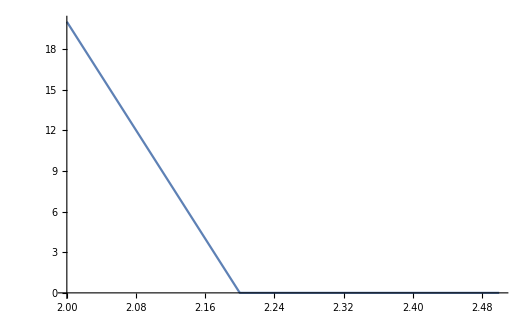

```mathematica
Plot[fppevharmonicrepulsive[k,r0,{x,0,0}-{0,0,0}][[1]],{x,2,2.5},PlotRange->Full]
```

====> pp_wormLike_spring

```mathematica
Clear[r,fppwormlikespring,fppwormlikespringMat,fppwormlikespringParticle];
r=N@3*{{Cos[Pi/3]*Sin[Pi/3],Cos[Pi/3]*Cos[Pi/3],Sin[Pi/3]},{0.,0.,0.},-{Cos[Pi/3]*Sin[Pi/3],Cos[Pi/3]*Cos[Pi/3],Sin[Pi/3]}}
```

{{1.29904,0.75,2.59808},{0.,0.,0.},{-1.29904,-0.75,-2.59808}}

```mathematica
fppwormlikespring[rij_]:=-a/(2*bk)*((1-(a*Norm[rij])/(bk*Nks))^-2-1+(4*a*Norm[rij])/(bk*Nks))*rij/Norm[rij](*rij = ri -rj*)
```

```mathematica
fppwormlikespringMat=Table[If[Abs[i-j]==1,fppwormlikespring[r[[i]]-r[[j]]],{0,0,0}],{i,1,Length@r},{j,1,Length@r}]
```

{{{0,0,0},{-0.110547,-0.0638244,-0.221094},{0,0,0}},{{0.110547,0.0638244,0.221094},{0,0,0},{-0.110547,-0.0638244,-0.221094}},{{0,0,0},{0.110547,0.0638244,0.221094},{0,0,0}}}

```mathematica
%//MatrixForm
```

((0
0
0) | (-0.110547
-0.0638244
-0.221094) | (0
0
0)
(0.110547
0.0638244
0.221094) | (0
0
0) | (-0.110547
-0.0638244
-0.221094)
(0
0
0) | (0.110547
0.0638244
0.221094) | (0
0
0))

```mathematica
fppwormlikespringParticle=Total[fppwormlikespringMat,{-2}]
```

{{-0.110547,-0.0638244,-0.221094},{0.,0.,0.},{0.110547,0.0638244,0.221094}}

```mathematica
%//MatrixForm
```

(-0.110547 | -0.0638244 | -0.221094
0. | 0. | 0.
0.110547 | 0.0638244 | 0.221094)

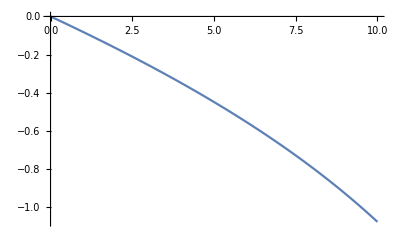

```mathematica
Plot[fppwormlikespring[{x,0,0}][[1]],{x,0,10}]
```

====> pp_constant_spring = ‘fx fy fz’

Easy to validate, no need to code here

====> pw_ev_empirical_polymerChain

(1) for dna_slit

```mathematica
Clear[boxMin,boxMax,r];
boxMin={-50,-50,-5};
boxMax={50,50,5};
r={{-47,-47,0},{47,47,0}};
dwall=bk*Nks^(1/2)/(2a);
yMin[ri_]:=ri-boxMin;
yMax[ri_]:=ri-boxMax;
```

```mathematica
fpwevempiricalpolymerChain[ri_]:=Table[If[Abs[yMin[ri][[j]]]<dwall,(25a)/bk(1-Abs[yMin[ri][[j]]]/dwall)^2,0]*(yMin[ri][[j]])/Abs[yMin[ri][[j]]]+If[Abs[yMax[ri][[j]]]<dwall,(25a)/bk(1-Abs[yMax[ri][[j]]]/dwall)^2,0](yMax[ri][[j]])/Abs[yMax[ri][[j]]],{j,1,3}]
```

```mathematica
Table[fpwevempiricalpolymerChain[r[[i]]],{i,1,Length@r}]
```

{{0.00763345,0.00763345,0},{-0.00763345,-0.00763345,0}}

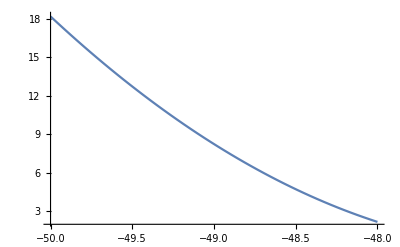

```mathematica
Plot[fpwevempiricalpolymerChain[{x,0,0}][[1]],{x,-50,-48}]
```

(2) for sphere

```mathematica
Clear[cavityRadius,r];
dwall=bk*Nks^(1/2)/(2a);
cavityRadius=50;
r=N@48*{-{Cos[Pi/3]*Sin[Pi/3],Cos[Pi/3]*Cos[Pi/3],Sin[Pi/3]},{Cos[Pi/3]*Sin[Pi/3],Cos[Pi/3]*Cos[Pi/3],Sin[Pi/3]}}
```

{{-20.7846,-12.,-41.5692},{20.7846,12.,41.5692}}

```mathematica
fpwevempiricalpolymerChainSphere[ri_]:=If[(cavityRadius-Norm[ri])≤dwall,(25a)/bk(1-(cavityRadius-Norm[ri])/dwall)^2*(-Normalize[ri]),{0,0,0}]
```

```mathematica
fpwevempiricalpolymerChainSphereMat=Table[fpwevempiricalpolymerChainSphere[r[[i]]],{i,1,Length@r}]
```

{{0.946865,0.546673,1.89373},{-0.946865,-0.546673,-1.89373}}

====> pw_ev_lj_cut = ‘epsilon sigma rcut’

(1) for slit

```mathematica
Clear[epsilon,sigma,rcut,r,boxMin,boxMax,fpwevljcut,fpwevljcutMinx];
epsilon=1;sigma=2.1;rcut=3.5;
r={-47.8,-47.8,0};
boxMin={-50,-50,-5};
boxMax={50,50,5};
```

```mathematica
fpwevljcut[epsilon_,sigma_,rcut_,rij_]:= If[Norm[rij]≤rcut,24*epsilon*(2*sigma^12/Norm[rij]^12-sigma^6/Norm[rij]^6)*rij/Norm[rij]^2,{0,0,0}];
```

```mathematica
fpwevljcutMinx=fpwevljcut[epsilon,sigma,rcut,{r[[1]]-boxMin[[1]],0,0}]
```

{4.23252,0.,0.}

(2) for sphere wall

```mathematica
Clear[cavityRadius,r,epsilon,sigma,rcut,r,boxMin,boxMax,fpwevljcut,fpwevljcutMinx];
epsilon=1;sigma=2.1;rcut=3.5;
cavityRadius=50;
r=N@48*{-{Cos[Pi/3]*Sin[Pi/3],Cos[Pi/3]*Cos[Pi/3],Sin[Pi/3]},{Cos[Pi/3]*Sin[Pi/3],Cos[Pi/3]*Cos[Pi/3],Sin[Pi/3]}}
```

{{-20.7846,-12.,-41.5692},{20.7846,12.,41.5692}}

```mathematica
riwall[ri_]:=-Normalize[ri]*(cavityRadius-Norm[ri]);
```

```mathematica
fpwevljcut[epsilon_,sigma_,rcut_,ri_]:= If[Norm[riwall[ri]]≤rcut,24*epsilon*(2*sigma^12/Norm[riwall[ri]]^12-sigma^6/Norm[riwall[ri]]^6)*riwall[ri]/Norm[riwall[ri]]^2,{0,0,0}];
```

```mathematica
fpwevljcutSphereMat=Table[fpwevljcut[epsilon,sigma,rcut,r[[i]]],{i,1,Length@r}]
```

{{11.6997,6.75485,23.3995},{-11.6997,-6.75485,-23.3995}}

====> pw_ev_lj_repulsive = ‘epsilon sigma’

(1) for slit

```mathematica
Clear[epsilon,sigma,rcut,r,boxMin,boxMax,fpwevljrepulsive,fpwevljrepulsiveMinx];
epsilon=1;sigma=2.1;rcut=sigma*2^(1/6);
r={-48,-48,0};
boxMin={-50,-50,-5};
boxMax={50,50,5};
```

```mathematica
fpwevljrepulsive[epsilon_,sigma_,rij_]:= If[Norm[rij]≤rcut,24*epsilon*(2*sigma^12/Norm[rij]^12-sigma^6/Norm[rij]^6)*rij/Norm[rij]^2,{0,0,0}];
```

```mathematica
fpwevljrepulsiveMinx=fpwevljrepulsive[epsilon,sigma,{r[[1]]-boxMin[[1]],0,0}]
```

{27.0194,0.,0.}

(2) for sphere

```mathematica
Clear[epsilon,sigma,rcut,r,boxMin,boxMax,fpwevljrepulsive,fpwevljrepulsiveMinx];
epsilon=1;sigma=2.1;
cavityRadius=50;
rcut=2^(1/6)*sigma;
r=N@48*{-{Cos[Pi/3]*Sin[Pi/3],Cos[Pi/3]*Cos[Pi/3],Sin[Pi/3]},{Cos[Pi/3]*Sin[Pi/3],Cos[Pi/3]*Cos[Pi/3],Sin[Pi/3]}}
```

{{-20.7846,-12.,-41.5692},{20.7846,12.,41.5692}}

```mathematica
riwall[ri_]:=-Normalize[ri]*(cavityRadius-Norm[ri]);
```

```mathematica
fpwevljcut[epsilon_,sigma_,ri_]:= If[Norm[riwall[ri]]≤rcut,24*epsilon*(2*sigma^12/Norm[riwall[ri]]^12-sigma^6/Norm[riwall[ri]]^6)*riwall[ri]/Norm[riwall[ri]]^2,{0,0,0}];
```

```mathematica
fpwevljrepulsiveSphereMat=Table[fpwevljcut[epsilon,sigma,r[[i]]],{i,1,Length@r}]
```

{{11.6997,6.75485,23.3995},{-11.6997,-6.75485,-23.3995}}

====> pw_ev_harmonic_repulsive

(1) for slit; easy to validate because f = -k x, it’s linear

(2) for sphere

```mathematica
r0=3.0;
k=1;
```

```mathematica
f1={0.433004,0.249995,0.866007}
r1=N@48*-{Cos[Pi/3]*Sin[Pi/3],Cos[Pi/3]*Cos[Pi/3],Sin[Pi/3]}
```

{0.433004,0.249995,0.866007}

{-20.7846,-12.,-41.5692}

```mathematica
Normalize[f1]
```

{0.433013,0.25,0.866025}

```mathematica
Normalize[r1]
```

{-0.433013,-0.25,-0.866025}